```mathematica
r[x_]:=Sqrt[x[[1]]^2+x[[2]]^2+x[[3]]^2];
```

```mathematica
X={Random[],Random[],Random[]}
```

{0.857774,0.811743,0.0131153}

```mathematica
r[X]
```

1.18105

```mathematica
LJPotential[x_]:=-1/r[x]^6+1/r[x]^12;
a={5,0,0};
LJForce[x_]:=6/r[x-a]^7-12/r[x-a]^13+6/r[x-a]^7-12/r[x-a]^13;
```

```mathematica
LJForce[X]
```

0.492693

```mathematica
a=5;
LJForce[x_]:=6/(x-a)^7-12/(x-a)^13+6/(x-a)^7-12/(x-a)^13;
```

```mathematica
s=NDSolve[{y''[x]==LJForce[x],y[0]==0.0,y'[0]==0},y,{x,-4,4}]
```

{{y→InterpolatingFunction[{{-4.,4.}},<>]}}

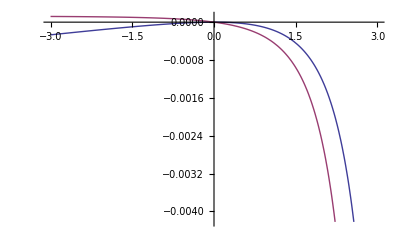

```mathematica
Plot[Evaluate[{y[x],y'[x]}/.s],{x,-3,3},PlotStyle->Automatic]
```